```mathematica
Vmorse[a_,re_,De_,r_]:=De (1-ⅇ^(-(r-re)/a))^2-De
```

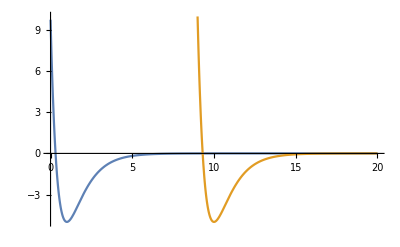

```mathematica
Plot[{Vmorse[1,1,5,r],Vmorse[1,10,5,r]},{r,0,20},PlotRange->{-5,10}]
```

```mathematica
sol=Solve[D[Vmorse[a,re,De,r],r]==0,r]
```

{{r→ConditionalExpression[re+2 ⅈ a π C[1],C[1]∈Integers]}}

```mathematica
Vmorse[a,re,De,re]
```

-De